OptionValue::nodef: Unknown option AppearanceRules for Dataset.

Expression | Time (s)
x^3 Erf[x]^2 | 0.000016
(x^7 - 24 x^4 - 4 x^2 + 8 x - 8)/(x^8 + 6 x^6 + 12 x^4 + 8 x^2) | 0.000017
(-4 x^2 - 4 x^3 - x^4)/((-1 + x^2)(1 + x + x^2)^2) | 9.×10^-6
x^3/(1 + x) | 3.×10^-6
(x^4 - 3 x^2 + 6)/(x^6 - 5 x^4 + 5 x^2 + 4) | 6.×10^-6
(-1 - E^x + E^x x Log[x])/((1 + E^x)^2 x) | 0.000012

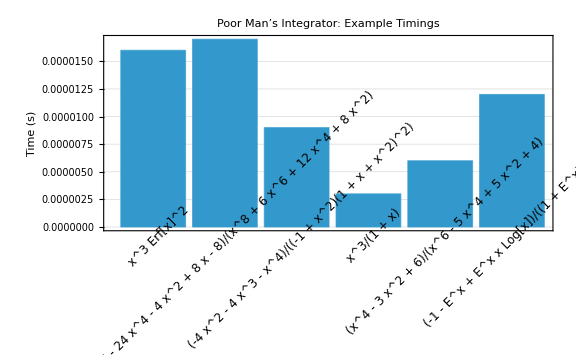

```mathematica
(*Define your raw timing data*)timings={{"x^3 Erf[x]^2",0.000016},{"(x^7 - 24 x^4 - 4 x^2 + 8 x - 8)/(x^8 + 6 x^6 + 12 x^4 + 8 x^2)",0.000017},{"(-4 x^2 - 4 x^3 - x^4)/((-1 + x^2)(1 + x + x^2)^2)",0.000009},{"x^3/(1 + x)",0.000003},{"(x^4 - 3 x^2 + 6)/(x^6 - 5 x^4 + 5 x^2 + 4)",0.000006},{"(-1 - E^x + E^x x Log[x])/((1 + E^x)^2 x)",0.000012}};

(*1) Interactive Dataset*)
Dataset[AssociationThread[{"Expression","Time (s)"},#]&/@timings,AppearanceRules-><|"HeaderBackground"->LightGray,"RowAlternation"->{White,LightYellow}|>]

(*2) Static styled Grid*)
Grid[Prepend[timings,{"Expression","Time (s)"}],Frame->All,Background->{None,{LightGray,{White}}},Alignment->{Left,Center},ItemStyle->{FontFamily->"Courier",FontSize->12}]

(*3) Bar chart with rotated labels*)
BarChart[timings[[All,2]],(*place the labels*below*the bars,rotated 45°*)ChartLabels->Placed[Rotate[#,45 Degree]&/@timings[[All,1]],Below],(*pick a single nice color,or a list of colors*)ChartStyle->RGBColor[0.2,0.6,0.8],ImageSize->Large,PlotTheme->"Detailed",AxesLabel->{None,"Time (s)"},PlotLabel->Style["Poor Man’s Integrator: Example Timings",14,Bold],LabelStyle->Directive[FontFamily->"Arial",FontSize->12],(*add light horizontal grid lines for readability*)GridLines->{None,Automatic},GridLinesStyle->Dashed]
```